### Introduction

My main goal when I came to the Wolfram Summer school was to create a project related to accessibility. From this wish, and from my mentoring process, the project theme emerged: textually describe wolfram language expressions based only in the symbolic structure of it. More precisely, my challenge would be to describe graphics expressions. In some way, this theme is related to accessibility, because the automatic generated texts could be used as alternative texts for this graphics, helping people with visual impairment, for example.

With the theme defined, I started working to find some path to create a general form of describing graphics. The first steps were to explore the already built-in functions that make similar things,  check the symbolic composition of graphics expressions and explore the wolfram language symbols properties. After that , I was secure enough about what path to follow.

Initially, I created functions to describe colors, and then, graphics primitives symbols (the main, but not the only, functions that can be used to create shapes in graphics). After some iterations of the project, it was decided to reduce the scope of it and initially describe more precisely the triangle shapes. From this point, I focused in creating specific functions to describe more properties related to this polygon. In the next sections, I explain in detail each part of this process, what I discovered on each of them, and the output related to my project.

### Wolfram Language symbols

I started my work by exploring the Wolfram Language symbols. In this phase, I discovered the WolframLanguageData function. This function provides informations about every symbol of the Wolfram Language. In special, this function allowed me to get the "functionality areas", the "translations" and the "documentation basic examples" properties for each symbol. These informations were important for the next steps. In this phase I learned that every symbol in the Wolfram Language also contains its related data, and this data can be used to say things, and to do things, with the own symbols. And that was the approach for this project - use the own informations about the symbols to describe expressions formed with them.

```mathematica
(*Getting every Wolfram Language symbol*)
WolframLanguageData[]//Length
```

5605

### Already built-in functions to describe Wolfram Language expressions

During the mentoring process, I saw that there are already some built-in functions to transform expressions into texts. The most famous one is the ToString function, but also there are the TextString and SpokenString. So, my next step were to check the output of each of these functions with a Graphics expression. And this was the result:

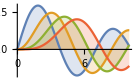
Graphics | ToString | TextString | SpokenString
-Graphics3D- | -Graphics3D- | Graphics3D[{RGBColor[1, 0, 0], Sphere[{0, 0, 0}]}] | a three-dimensional graphic consisting of a sphere
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of 11 polygons, a line connecting 574 points, a line connecting 541 points, a line connecting 556 points and a line connecting 610 points
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of 103 arrows and 103 disks

As it can be seen, the most human-readable version was the SpokenString function output. Even this, there are some cases in which it doesn’t bring a meaningful description, like in the second and third cases - it probably wouldn’t be possible to have a clear idea of the figure only with the texts. Also, it discards some aspects of the figure, like the color. Because of that, it was decided that the first small step would be to describe colors, for then integrate it into a more complete description function for graphics.

In this part I also created two functions to describe any wolfram language symbol - Description, to get the name of it; and TranslatedDescription, to get the translated name of it. Both of them use the WolframLanguageData presented previously. Here are some tests:

```mathematica
someWLSymbols={List,Table,Range,Graphics,Image,ColorQ,Number,Grid,Entity,Values,Map,Thread,Function, MapThread};

symbolDescriptionTests=Block[
{descriptions=Description@someWLSymbols,spanish,portuguese,japanese},
spanish=TranslatedDescription[someWLSymbols,"Spanish"];
portuguese=TranslatedDescription[someWLSymbols,"Portuguese"];
japanese=TranslatedDescription[someWLSymbols,"Japanese"];
MapThread[{#1,#2,#3,#4,#5}&,{someWLSymbols,descriptions,spanish,portuguese,japanese}]
];

Grid[PrependTo[symbolDescriptionTests,Style[#,Bold]&/@{"Original","Description","Spanish","Portuguese","Japanese"}],Frame->All]
```

Original | Description | Spanish | Portuguese | Japanese
List | List | lista | lista | リスト
Table | Table | tabla | tabela | リストを作成
Range | Range | rango | intervalo de valores | 範囲
Graphics | Graphics | gráfico | representação gráfica | グラフィックス
Image | Image | imagen | imagem | 画像
ColorQ | Color Q | ¿color? | Cor? | 色かどうか
Number | Number | número | número | 数
Grid | Grid | rejilla | grade | 格子
Entity | Entity | entidad | entidade | 実体
Values | Values | valores | lista de valores de associação | 値
Map | Map | aplica a todos | aplica-se ao primeiro nível | 適用
Thread | Thread | atraviesa | através das listas | 縫い込む
Function | Function | función | função | 関数
MapThread | Map Thread | aplica a través | aplica à ligação de elementos correspondentes | 縫込み適用

### Describing colors

Before starting describing colors, I discovered that the Wolfram Language have a set of named colors. These colors are the most common ones, and each has its own symbol in the Wolfram Language. Each of these symbols also have its own informations. My first objective was to filter, among all the symbols, the ones that are named colors. Once I had it, the idea was to create a function that would receive any RGBColor expression, compare it with all the named colors that I found, and return the name of the closest color.

For filtering the named colors among the Wolfram Language symbols, I saw that the "functionality areas" property for these symbols always was the value ColorSymbols. With that, I just filtered all the symbols that had this value for the cited property, and checked if they were a colors using the ColorQ function.

```mathematica
(*Getting the `functionality areas` property for the Red color.*)
EntityValue[WolframLanguageData["Red"], EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]
```

{ColorSymbols}

```mathematica
(*Filtering every named color among the Wolfram Language symbols, based on the `functionality areas` property.*)
functionalityAreasOfAllWLSymbols=MapThread[{#1,#2}&,{WolframLanguageData[],EntityValue[WolframLanguageData[],EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]}];
colorSymbols=Select[functionalityAreasOfAllWLSymbols, (Length@Last@#)==1&&((First@Last@#)=="ColorSymbols")&]⟦All,1⟧;
namedColors= Select[colorSymbols,ColorQ@RGBColor@#["Name"]&]
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightCyan,LightGreen,LightPink,LightYellow,Magenta,Orange,Pink,Purple,Red,White,Yellow}

After that I needed to address the problem of calculating the similarity between two RGBColor expressions. My idea was to create a function the get the average of the differences of each color channel. For that, I created the ColorDistanceByAverage functions (I ended up not using this implementation in my final color description function because the built-in Nearest function uses the Euclidean distance by default).

```mathematica
ColorDistanceByAverage[color1_RGBColor,color2_RGBColor]:=N[Mean[MapThread[Abs[#1-#2]&,{List@@color1,List@@color2}]]]
```

```mathematica
ColorDistanceByAverage[Red,#]&/@{Red,Green,Blue,Pink}
```

{0.,0.666667,0.666667,0.333333}

Then, I created the Description function for RBGColor expressions. I also created the TransletedDescription version of it, that works similar to the TransletedDescription for symbols.

```mathematica
Description[color_RGBColor]:=Block[
{colors=<|RGBColor[0., 0., 0.]->Entity["WolframLanguageSymbol","Black"],RGBColor[0., 0., 1.]->Entity["WolframLanguageSymbol","Blue"],RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]->Entity["WolframLanguageSymbol","Brown"],RGBColor[0., 1., 1.]->Entity["WolframLanguageSymbol","Cyan"],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]->Entity["WolframLanguageSymbol","Gray"],RGBColor[0., 0.5019607843137255, 0.]->Entity["WolframLanguageSymbol","Green"],RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]->Entity["WolframLanguageSymbol","LightBlue"],RGBColor[0.87843137254902, 1., 1.]->Entity["WolframLanguageSymbol","LightCyan"],RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]->Entity["WolframLanguageSymbol","LightGreen"],RGBColor[1., 0.7137254901960784, 0.7568627450980392]->Entity["WolframLanguageSymbol","LightPink"],RGBColor[1., 1., 0.87843137254902]->Entity["WolframLanguageSymbol","LightYellow"],RGBColor[1., 0., 1.]->Entity["WolframLanguageSymbol","Magenta"],RGBColor[1., 0.6470588235294118, 0.]->Entity["WolframLanguageSymbol","Orange"],RGBColor[1., 0.7529411764705882, 0.796078431372549]->Entity["WolframLanguageSymbol","Pink"],RGBColor[0.5019607843137255, 0., 0.5019607843137255]->Entity["WolframLanguageSymbol","Purple"],RGBColor[1., 0., 0.]->Entity["WolframLanguageSymbol","Red"],RGBColor[1., 1., 1.]->Entity["WolframLanguageSymbol","White"],RGBColor[1., 1., 0.]->Entity["WolframLanguageSymbol","Yellow"]|>,similar,entity},
similar=First@Nearest[Keys@colors,color,1];
entity=colors@similar;
Description[color]=ResourceFunction["FromCamelCase"]@entity@"Name"
]

outputComparations=With[{color=RGBColor@#},
{color,ToString@color,TextString@color,SpokenString@color,Description@color}]&/@RandomReal[1,{10,3}];

Grid[PrependTo[outputComparations,Style[#,Bold]&/@{"RGB color","ToString","TextString","SpokenString","Description"}],Frame->All]
```

RGB color | ToString | TextString | SpokenString | Description
RGBColor[{0.13834638211441952, 0.10944037874548829, 0.09705518183954887}] | RGBColor[{0.138346, 0.10944, 0.0970552}] | RGBColor[{0.138346, 0.10944, 0.0970552}] | RGB color 0.138, 0.109, 0.097 | Black
RGBColor[{0.6998114874500838, 0.013106753310190289, 0.7453896078041529}] | RGBColor[{0.699811, 0.0131068, 0.74539}] | RGBColor[{0.699811, 0.0131068, 0.74539}] | RGB color 0.7, 0.013, 0.745 | Purple
RGBColor[{0.41098744104091556, 0.8671517747586834, 0.6623246833367291}] | RGBColor[{0.410987, 0.867152, 0.662325}] | RGBColor[{0.410987, 0.867152, 0.662325}] | RGB color 0.411, 0.867, 0.662 | Light Green
RGBColor[{0.6371560959968514, 0.7985979800330758, 0.2571355735647842}] | RGBColor[{0.637156, 0.798598, 0.257136}] | RGBColor[{0.637156, 0.798598, 0.257136}] | RGB color 0.637, 0.799, 0.257 | Light Green
RGBColor[{0.548304732640936, 0.725850133023968, 0.1819235574702489}] | RGBColor[{0.548305, 0.72585, 0.181924}] | RGBColor[{0.548305, 0.72585, 0.181924}] | RGB color 0.548, 0.726, 0.182 | Green
RGBColor[{0.8818156401069392, 0.47620256378328363, 0.10674904138416186}] | RGBColor[{0.881816, 0.476203, 0.106749}] | RGBColor[{0.881816, 0.476203, 0.106749}] | RGB color 0.882, 0.476, 0.107 | Orange
RGBColor[{0.29500412829881206, 0.9079955791864953, 0.7014883513816168}] | RGBColor[{0.295004, 0.907996, 0.701488}] | RGBColor[{0.295004, 0.907996, 0.701488}] | RGB color 0.295, 0.908, 0.701 | Light Green
RGBColor[{0.43979550971980985, 0.3546381234991267, 0.012921790905866759}] | RGBColor[{0.439796, 0.354638, 0.0129218}] | RGBColor[{0.439796, 0.354638, 0.0129218}] | RGB color 0.44, 0.355, 0.013 | Gray
RGBColor[{0.10609572752463148, 0.9630025658230474, 0.8666665284503903}] | RGBColor[{0.106096, 0.963003, 0.866667}] | RGBColor[{0.106096, 0.963003, 0.866667}] | RGB color 0.106, 0.963, 0.867 | Cyan
RGBColor[{0.8443134928309199, 0.9344760613670275, 0.11019104425074921}] | RGBColor[{0.844313, 0.934476, 0.110191}] | RGBColor[{0.844313, 0.934476, 0.110191}] | RGB color 0.844, 0.934, 0.11 | Yellow

When compared with the built-in functions output, it can be said that the created function represents an improvement to describe colors. This part of the project was important to validate the path I was following by showing concrete results. Following, the version to return translated texts, and some examples.

```mathematica
TranslatedDescription[color_RGBColor,language_String]:=Block[
{colors=<|RGBColor[0., 0., 0.]->Entity["WolframLanguageSymbol","Black"],RGBColor[0., 0., 1.]->Entity["WolframLanguageSymbol","Blue"],RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]->Entity["WolframLanguageSymbol","Brown"],RGBColor[0., 1., 1.]->Entity["WolframLanguageSymbol","Cyan"],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]->Entity["WolframLanguageSymbol","Gray"],RGBColor[0., 0.5019607843137255, 0.]->Entity["WolframLanguageSymbol","Green"],RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]->Entity["WolframLanguageSymbol","LightBlue"],RGBColor[0.87843137254902, 1., 1.]->Entity["WolframLanguageSymbol","LightCyan"],RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]->Entity["WolframLanguageSymbol","LightGreen"],RGBColor[1., 0.7137254901960784, 0.7568627450980392]->Entity["WolframLanguageSymbol","LightPink"],RGBColor[1., 1., 0.87843137254902]->Entity["WolframLanguageSymbol","LightYellow"],RGBColor[1., 0., 1.]->Entity["WolframLanguageSymbol","Magenta"],RGBColor[1., 0.6470588235294118, 0.]->Entity["WolframLanguageSymbol","Orange"],RGBColor[1., 0.7529411764705882, 0.796078431372549]->Entity["WolframLanguageSymbol","Pink"],RGBColor[0.5019607843137255, 0., 0.5019607843137255]->Entity["WolframLanguageSymbol","Purple"],RGBColor[1., 0., 0.]->Entity["WolframLanguageSymbol","Red"],RGBColor[1., 1., 1.]->Entity["WolframLanguageSymbol","White"],RGBColor[1., 1., 0.]->Entity["WolframLanguageSymbol","Yellow"]|>,similar,entity,lang,translations},
similar=First@Nearest[Keys@colors,color,1];
entity=colors@similar;
lang=Entity["Language",language];
translations=Association[entity@"Translations"];
TranslatedDescription[color,language]=ResourceFunction["FromCamelCase"]@translations@lang
]

colorTranslationTests={
#, Style[Description@#,#],
Style[TranslatedDescription[#,"Spanish"],#],
Style[TranslatedDescription[#,"Portuguese"],#],
Style[TranslatedDescription[#,"Japanese"],#]}&/@RGBColor/@RandomReal[1,{10,3}];

Grid[PrependTo[colorTranslationTests,Style[#,Bold]&/@{"RGB Color","English","Spanish","Portuguese","Japanese"}],Frame->All,Alignment->Left]
```

RGB Color | English | Spanish | Portuguese | Japanese
RGBColor[{0.5315508423688435, 0.8963071160423999, 0.08447860222293757}] | Light Green | verde claro | verde claro | 薄緑色
RGBColor[{0.8562436874347557, 0.893878676250859, 0.9084928333204632}] | White | blanco | branco | 白
RGBColor[{0.078990535524045, 0.2047584826132307, 0.9728208319859564}] | Blue | azul | azul | 青
RGBColor[{0.13184733619671873, 0.3559323783015158, 0.9632163441824413}] | Blue | azul | azul | 青
RGBColor[{0.32261583418055184, 0.6428518478739196, 0.2411705809881679}] | Green | verde | verde | 緑
RGBColor[{0.903279482578941, 0.29128764519587347, 0.9627255998789606}] | Magenta | magenta | magenta | マジェンタ色
RGBColor[{0.33752208400869743, 0.14683940761731473, 0.21909170395070832}] | Black | negro | preto | 黒
RGBColor[{0.4460312710483445, 0.6652266938300524, 0.7588244456181577}] | Light Blue | azul claro | azul claro | 水色
RGBColor[{0.10859052562981009, 0.42251186083727865, 0.2091899403102908}] | Green | verde | verde | 緑
RGBColor[{0.22433340366812882, 0.9301433802623331, 0.6934793545924998}] | Light Green | verde claro | verde claro | 薄緑色

### Describing graphics

The Graphics symbol in the Wolfram Language is a very flexible function, allowing dozens of configurations. It can be composed of primitives, directives, wrappers, options and method. For my project I decided to start with the primitives. This way, the first step of this sections was, as in the color description initial approach, to get every Wolfram Language symbol that are graphics primitives. The filter also is made with the "functionality areas" property, but now for the values equal to GraphicsPrimitiveSymbols.

```mathematica
(*Filtering every garphics primitives among the Wolfram Language symbols, based on the `functionality areas` property.*)
```

```mathematica
graphicsPrimitiveSymbols=Select[functionalityAreasOfAllWLSymbols,Count[Last@#,"GraphicsPrimitiveSymbols"]>0&];
graphicsSymbols=graphicsPrimitiveSymbols⟦All,1⟧
graphicsSymbols//Length
```

{AASTriangle,ASATriangle,AffineHalfSpace,AffineSpace,Annulus,Arrow,BSplineCurve,Ball,BezierCurve,CapsuleShape,Circle,Circumsphere,Cone,ConicHullRegion,Cube,Cuboid,Cylinder,DiskSegment,Dodecahedron,Ellipsoid,EmptyRegion,FilledCurve,FullRegion,GraphicsComplex,HalfLine,HalfPlane,HalfSpace,Hexahedron,Hyperplane,Icosahedron,InfiniteLine,InfinitePlane,Insphere,JoinedCurve,Octahedron,Parallelepiped,Parallelogram,Polyhedron,Prism,Rectangle,RegularPolygon,SASTriangle,SSSTriangle,ShellRegion,Simplex,Sphere,SphericalShell,StadiumShape,Tetrahedron,Triangle,Tube}

51

This, beyond allowing me to create the related Description and TranslatedDescription functions specifically for the graphics primitives symbols (they were created right after that), also allowed me to have a better notion of the project’s scope. After that I also created the GraphicsPrimtiveQ function to identify if a given string, symbol or expression represents a graphics primitive or not.

Here, the "documentation basic examples"  property was very useful. This property contains lots of ready examples to each symbol. The examples for the graphics primitives symbols was used for tests during the development. Without that I would have to create much more extra code for the tests.

```mathematica
(*Getting an example of use for the Rectangle symbol.*)
EntityValue[Entity["WolframLanguageSymbol","Rectangle"],EntityProperty["WolframLanguageSymbol","DocumentationBasicExamples"]]⟦4⟧
```

{Differently styled rectangles:,{Graphics[{Pink,Rectangle[]}],Graphics[{EdgeForm[Thick],Pink,Rectangle[]}],Graphics[{EdgeForm[Dashed],Pink,Rectangle[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Rectangle[]}]},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

The next step was to create a function to finally describe a Graphics expression. So, I did it. The created function is capable of describing a Graphics expression in terms of graphics primitives symbols and colors.

```mathematica
Description[graphics_Graphics]:=Block[
{elements,primitives,sorted,descriptions},
elements=Flatten[List@@graphics];
primitives=Select[elements,(ColorQ@#||GraphicsPrimitiveQ@#)&];
sorted=Sort[#,ColorQ@#1&]&/@Partition[primitives,2];
descriptions=ToLowerCase[Description[#]]&/@sorted;
"A graphic consisting of "<>ToString@Row[Row[#," "]&/@descriptions, ", "]<>"."
]
```

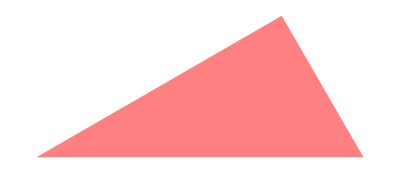
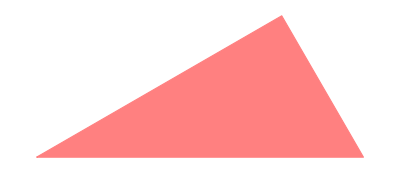
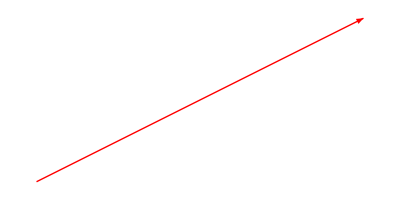
```mathematica
someGraphics={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
InputForm/@someGraphics
Grid[PrependTo[{#,ToString@#,TextString@#,SpokenString@#,Description@#}&/@someGraphics,Style[#,Bold]&/@{"Graphics","ToString","TextString","SpokenString","Description"}],Frame->All]
```

{Graphics[{RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}],Graphics[{RGBColor[1, 0.5, 0.5], EdgeForm[Thickness[Large]], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}],Graphics[{RGBColor[1, 0, 0], AffineHalfSpace[{0, 0}, {{1, -1}}, {1, 1}]}],Graphics[{RGBColor[0, 1, 0], AffineSpace[{0, 0}, {{1, -1}}]}],Graphics[{RGBColor[1, 0.5, 0.5], Annulus[{0, 0}, {1/2, 1}]}],Graphics[{RGBColor[1, 0, 0], {Arrowheads[Large], Arrow[{{0, 0}, {1, 0.5}}]}}]}

Graphics | ToString | TextString | SpokenString | Description
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0.5, 0.5 and Triangle of the list the list 0, 0, the list 2, 0, the list 3 halves, 1 half times square root of 3 | A graphic consisting of light pink triangle.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0.5, 0.5, edge form thickness Large and Triangle of the list the list 0, 0, the list 1, 0, the list 3 fourths, 1 fourth times square root of 3 | A graphic consisting of light pink triangle.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0, 0 and AffineHalfSpace of the list 0, 0, the list the list 1, minus 1 and the list 1, 1 | A graphic consisting of red affine half space.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0, 1, 0 and AffineSpace of the list 0, 0 and the list the list 1, minus 1 | A graphic consisting of light green affine space.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 1, 0.5, 0.5 and Annulus of the list 0, 0 and the list 1 half, 1 | A graphic consisting of light pink annulus.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of an arrow | A graphic consisting of red arrow.

Despite its limitation, the Description function for Graphics also presents an improvement for the generated text. From this point, the next steps were to continue improving the description functions to add more characteristics of the expressions. Because of the great amount of primitives, the focus was given to a single one - the triangle. This way, the next improvements of the project were related to describing these polygons in more details.

### Working with triangles

The initial goal was to identify and say the type of triangle that is being displayed (right, equilateral, isosceles, scalene and obtuse). To achieve that, initially I created some auxiliary functions:

TrianglePointsQ : receives a list of points of the same dimension and returns if it forms a triangle or not.

TrianglePolygonQ: receives a triangle Polygon expression and returns if it is a triangle or not.

TriangleQ: is a generalization of the two previous ones. It can receive both a list of points of the same dimension or a polygon, and return if they are a triangle or not.

Later on, I created a TriangleTypeQ function for each triangle type. All of them receives a triangle polygon and returns if it is of the given type or not. The name of the created functions are: TriangleRightQ, TriangleEquilateralQ, TriangleIsoscelesQ, TriangleScaleneQ and TriangleObtuseQ. Following, some usage examples:

```mathematica
triangles={Triangle[],AASTriangle[Pi/6,Pi/3,1],SSSTriangle[3,4,5],SASTriangle[1,Pi/2,2],ASATriangle[Pi/6,1,Pi/3],Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}],Polygon[{{0,0},{10,10},{10,20}}],RandomPolygon@3};

triangleQs={TrianglePolygonQ,TriangleRightQ,TriangleEquilateralQ,TriangleIsoscelesQ,TriangleScaleneQ,TriangleObtuseQ};

triangleTests=Function[
triangle,
Flatten[
{{Graphics@triangle,
N[#/Degree]&/@PolygonAngle[triangle],
N@*EuclideanDistance@@#&/@Subsets[First[List@@triangle],{2}]},
With[
{answer=#[triangle]},
Style[TextString[answer,BooleanStrings-> {"Yes","No" }],If[answer,Blue,Red]]
]&/@triangleQs},
1
]
]/@triangles;

Grid[PrependTo[triangleTests,
Style[#,Bold]&/@{"Graphics","Interior angles","Side lengths", "Triangle?", "Right?", "Equilateral?","Isosceles?","Scalene?","Obtuse?"}],Frame->All]
```

Graphics | Interior angles | Side lengths | Triangle? | Right? | Equilateral? | Isosceles? | Scalene? | Obtuse?
-Graphics- | {90.,45.,45.} | {1.,1.,1.41421} | Yes | Yes | No | Yes | No | No
-Graphics- | {30.,60.,90.} | {2.,1.73205,1.} | Yes | Yes | No | No | Yes | No
-Graphics- | {36.8699,53.1301,90.} | {5.,4.,3.} | Yes | Yes | No | No | Yes | No
-Graphics- | {26.5651,63.4349,90.} | {2.23607,2.,1.} | Yes | Yes | No | No | Yes | No
-Graphics- | {30.,60.,90.} | {1.,0.866025,0.5} | Yes | Yes | No | No | Yes | No
-Graphics- | {60.,60.,60.} | {2.,2.,2.} | Yes | No | Yes | Yes | No | No
-Graphics- | {18.4349,135.,26.5651} | {14.1421,22.3607,10.} | Yes | No | No | No | Yes | Yes
-Graphics- | {305.923,261.548,332.529} | {0.530581,0.648081,0.302243} | Yes | No | No | No | Yes | Yes

With these functions I was already able to describe the triangles classification. To help me with this process, I created the TriangleCharacteristics function. This function receives a triangle polygon and returns a list of string with the name of each characteristic of the given triangle.

```mathematica
TriangleCharacteristics[triangle_]:=With[
{rules=<|TriangleRightQ-> "Right",TriangleEquilateralQ-> "Equilateral",TriangleIsoscelesQ-> "Isosceles",TriangleScaleneQ-> "Scalene",TriangleObtuseQ-> "Obtuse"|>},
Select[Keys@rules,#@triangle&]/.rules
]/;TriangleQ@triangle

TriangleCharacteristics/@triangles
```

{{Right,Isosceles},{Right,Scalene},{Right,Scalene},{Right,Scalene},{Right,Scalene},{Equilateral,Isosceles},{Scalene,Obtuse},{Scalene,Obtuse}}

Now, I need to describe one more thing about triangles: the orientation of the greatest side (is it a vertical, horizontal or diagonal line?). For doing so, it was necessary to develop an algorithm composed of three steps: 1) find the coordinates of the greatest side of a triangle, 2) get the inclination of this line and 3) decide the orientation of this line. For the first step, I created the TriangleGreatestSide function. Bellow, its definition and some examples.

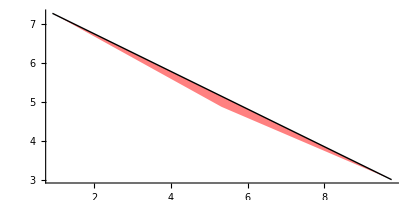
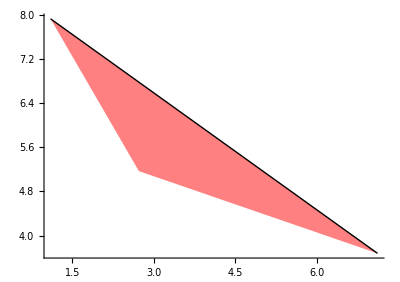
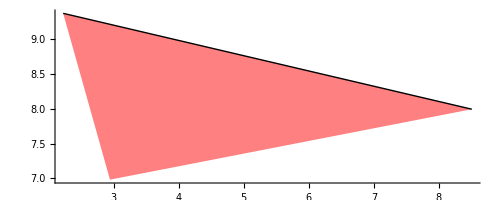
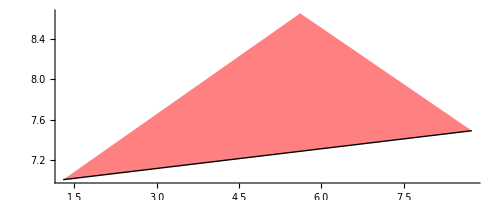
Greatest side coordinates | Triangle plot with the greates side
{{0.907494,7.26218},{9.75485,3.00329}} | -Graphics-
{{3.31056,8.43568},{4.62458,3.41327}} | -Graphics-
{{1.0978,7.92275},{7.1135,3.67798}} | -Graphics-
{{2.22301,9.3761},{8.50698,7.99443}} | -Graphics-
{{1.29424,7.00479},{8.74153,7.48903}} | -Graphics-

```mathematica
TriangleGreatestSide[triangle_]:=Block[
{coordinates,sides,lengths,greatestSideCoordinate},
coordinates=PolygonCoordinates@triangle;
sides=Subsets[coordinates,{2}];
lengths={#,N@*EuclideanDistance@@#}&/@sides;
greatestSideCoordinate=Sort[lengths,Last@#1>Last@#2&]⟦1,1⟧;
greatestSideCoordinate
]/;TrianglePolygonQ@triangle

sideTests=With[
{side=TriangleGreatestSide@#},
{side,Graphics[{Pink,#,Black,Thick,Line@side},Axes->True]}
]&/@Polygon/@RandomReal[10,{5,3,2}];

Grid[PrependTo[sideTests,Style[#,Bold]&/@{"Greatest side coordinates", "Triangle plot with the greates side"}],Frame->All]
```

To define the orientation of the greatest side I defined some angle regions for each possible orientation. For that, the trigonometric circle was divided in 32 small parts, with 4 of them to the horizontal orientation, other 4 to the vertical orientation and the rest to the diagonal orientation. Being this, any line that has the inclination that is inside of one of this regions is going to be considered in the respective orientation. The next figure illustrates each of these regions.

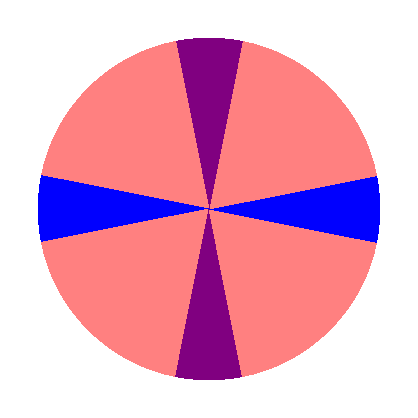
Regions to define the orientation of the greatest side of a triangle.
-Graphics-
Blue = Horizontal
Purple = Vertical
Pink = Diagonal

After getting the greatest side coordinates, I create another point, with the  x coordinate from the second point, and the y coordinate from first point. With this new point, and with the previous ones I create another triangle, and get the internal angle formed at the first point of this triangle. This angle gives me the inclination of the greatest side of the triangle. So this I can properly classify the orientation using my sectioned trigonometric circle. Bellow, I show the functions to each of this processes (Angle and AngleOrientation), and also some auxiliary plots.

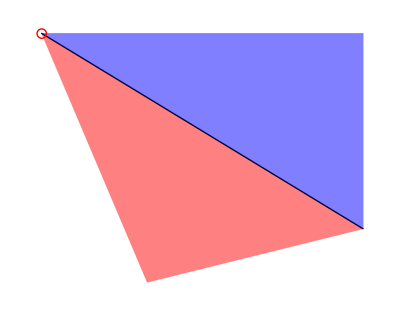
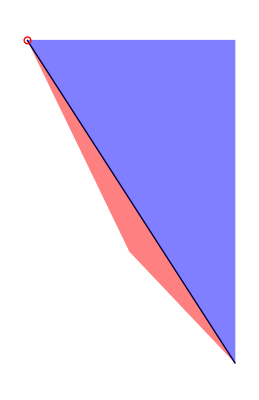
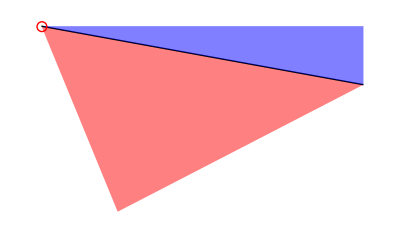
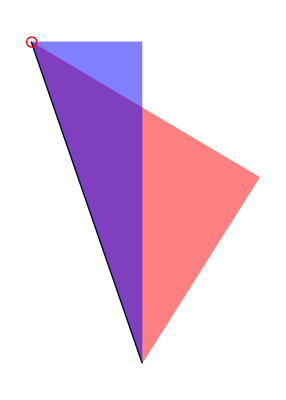
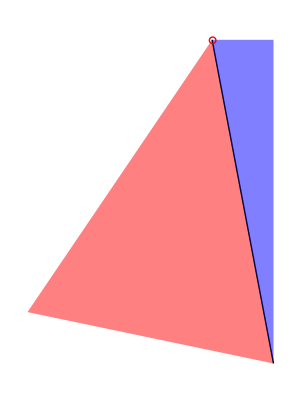
Original triangle (pink)
Auxiliar triangle (blue)
Greatest side (black line)
Angle (red circle) | Angle | Greatest side orientaiton
-Graphics- | 31.3503 | Diagonal
-Graphics- | 57.2153 | Diagonal
-Graphics- | 10.3197 | Horizontal
-Graphics- | 70.9265 | Diagonal
-Graphics- | 79.2349 | Diagonal

```mathematica
Angle[a_List,b_List]:=With[{c={b⟦1⟧,a⟦2⟧}},N@PlanarAngle[{b,a,c}]]/;Dimensions[a]==Dimensions[b]=={2}
Angle[points_List]:=Angle[First[points],Last[points]]

AngleOrientation[angle_Real]:=Block[
{normalized,possibilities,orientations=<|0.->"Horizontal",0.19634954084936207->"Horizontal",3.141592653589793->"Horizontal",3.3379421944391554->"Horizontal",6.283185307179586->"Horizontal",1.5707963267948966->"Vertical",1.7671458676442586->"Vertical",4.71238898038469->"Vertical",4.908738521234052->"Vertical",0.39269908169872414->"Diagonal",0.5890486225480862->"Diagonal",0.7853981633974483->"Diagonal",0.9817477042468103->"Diagonal",1.1780972450961724->"Diagonal",1.3744467859455345->"Diagonal",1.9634954084936207->"Diagonal",2.1598449493429825->"Diagonal",2.356194490192345->"Diagonal",2.552544031041707->"Diagonal",2.748893571891069->"Diagonal",2.945243112740431->"Diagonal",3.5342917352885173->"Diagonal",3.730641276137879->"Diagonal",3.9269908169872414->"Diagonal",4.123340357836604->"Diagonal",4.319689898685965->"Diagonal",4.516039439535327->"Diagonal",5.105088062083414->"Diagonal",5.301437602932776->"Diagonal",5.497787143782138->"Diagonal",5.6941366846315->"Diagonal",5.890486225480862->"Diagonal",6.086835766330224->"Diagonal"|>},
If[angle>2.Pi,normalized=Mod[angle,2.Pi],normalized=angle];
orientations@First@Nearest[Keys@orientations,normalized]
]

sideTests=With[
{side=TriangleGreatestSide@#},
{Graphics[{
Pink,#,
Black,Thick,Line@side,
Blue,Opacity@.5,Triangle[Append[side,{Last[side]⟦1⟧,First[side]⟦2⟧}]],
Red,Opacity@1.,Circle[First@side,0.1]
}],
N[Angle@side/Degree],
AngleOrientation@Angle@side}
]&/@Polygon/@RandomReal[10,{5,3,2}];

Grid[PrependTo[sideTests,Style[#,Bold]&/@{"Original triangle (pink)\nAuxiliar triangle (blue)\nGreatest side (black line)\nAngle (red circle)","Angle","Greatest side orientaiton"}],Frame->All]
```

The last step was to put all the functions related to triangles into a single functions capable of describing triangles in a Graphics expression, returning a human-readable string.  For this task I created the following code, that produces the results at the end.

```mathematica
StringList[list_List]:=With[{str=Row[ToLowerCase@list,", "]},
StringReplace[rest__~~", "~~s__~~EndOfString:> rest<>" and "<>s]@ToString[str]]

TriangleDescription[triangle_]:=Block[{characteristics,side,sidestr},
characteristics=StringList@TriangleCharacteristics@triangle;
side=AngleOrientation@Angle@TriangleGreatestSide@triangle;
sidestr=If[Not[TriangleEquilateralQ@triangle]," triangle, with its greatest side as a "<>ToLowerCase[side]<>" line"," triangle"];
characteristics<>sidestr]/;SimplePolygonQ@triangle

TriangleDescription[graphics_Graphics]:=Block[{primitivesAndDirectives,color,triangleDescription},
primitivesAndDirectives=graphics/.Graphics[arguments_List,___]:>  arguments;
color=ToLowerCase[Description[Select[primitivesAndDirectives,ColorQ]//First]];
triangleDescription=TriangleDescription[Select[primitivesAndDirectives,TrianglePolygonQ]//First];
"A graphic consisting of a "<>color<>", "<>triangleDescription<>"."]

triangleDescriptionTests=Block[{color,graphics},
color=RGBColor@RandomReal[1,{3}];
graphics=Graphics[{color,#}];
{graphics,ToString@graphics,TextString@graphics,SpokenString@graphics,TriangleDescription@graphics}]&/@triangles;
Grid[PrependTo[triangleDescriptionTests,Style[#,Bold]&/@{"Graphics","ToString","TextString","SpokenString","TriangleDescription"}],Frame->All]
```

Graphics | ToString | TextString | SpokenString | TriangleDescription
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.011, 0.974, 0.156 and Triangle of the list the list 0, 0, the list 1, 0, the list 0, 1 | A graphic consisting of a light green, right and isosceles triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.917, 0.157, 0.193 and Triangle of the list the list 0, 0, the list 2, 0, the list 3 halves, 1 half times square root of 3 | A graphic consisting of a red, right and scalene triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.465, 0.007, 0.093 and Triangle of the list the list 0, 0, the list 5, 0, the list 16 fifths, 12 fifths | A graphic consisting of a brown, right and scalene triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.686, 0.281, 0.977 and Triangle of the list the list 0, 0, the list square root of 5, 0, the list 4 times one over square root of 5, 2 times one over square root of 5 | A graphic consisting of a magenta, right and scalene triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of RGB color 0.66, 0.275, 0.915 and Triangle of the list the list 0, 0, the list 1, 0, the list 3 fourths, 1 fourth times square root of 3 | A graphic consisting of a magenta, right and scalene triangle, with its greatest side as a horizontal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a orange, equilateral and isosceles triangle.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a gray, scalene and obtuse triangle, with its greatest side as a diagonal line.
-Graphics- | -Graphics- | Graphics[…] | a graphic consisting of a polygon with 3 vertices | A graphic consisting of a light green, scalene triangle, with its greatest side as a diagonal line.

It is important to note that for equilateral triangles the greatest side orientation is not being described, because all the sides are equal.

The complete implementation can be find in the link: https://github.com/rsg73626/wss-project

### Conclusion and future works

This project presented a challenging task, with a very large scope of implementation. In this first step, some important progress was made related to textually describing Wolfram Language expressions, in special for Graphics, and for triangle figures. Following, some of the future works that can be done.

Merge the Description and TranslatedDescription functions for symbols into a single one that can receive the language as an option.

Merge the Description and TranslatedDescription functions for colors into a single one that can receive the language as an option.

Improve the Description function implementation for graphics, so this it can support more graphics primitives, and also the other components of the Graphics expressions.

Enhance the Description function implementation for graphics, so this it also can describe points and lines plots properly.

Put the TriangleDescription function inside a more generic Description function that supports any type of polygon.

Increase the scope of the project for other types of expressions.

Test the output quality for the description functions for graphics and triangles.

Create functions and/or applications that can be used with visually impaired people. For example , an application to help with the geometry teaching.